eigenState defined

1

ρ0[r]

(75 ρ0[r])/π

ρ defined

eqn for m defined

condition for m defined

eqn for p defined

condition for p defined

ρ2=ρ0[1]

System defined

NDSolve`StateData[<0.0001>]

Rstar=1.km

Rmax=rMaxkm

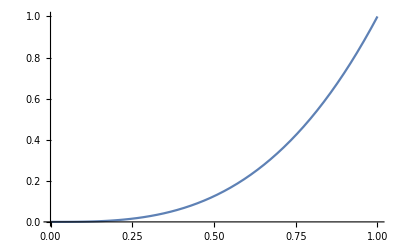

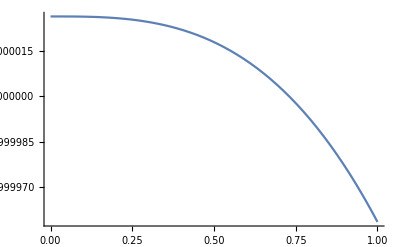

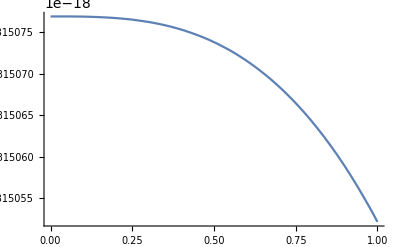

Radius=rMax

Mass=InterpolatingFunction[{{0.0001, 1.}}, <>][rMax]

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
G:=6.67408*10^(-11)(*gravitational constant in SI units*)
c:=299792458(*speed of light in SI units*)
(*m[r]:=4/3 π r^3 ρ0*)
my0:=10^(-4);
κ:=0.3
RSun :=1;
MSun:=100;
rsSun:=2G*MSun/(c^2)
ρSun:=3 MSun/(4 π RSun^3);
Print["eigenState defined"];

(*d[my0]:=2;*)
(*K=c^2/(ρSun^(κ-1))*)
K=1

d[r_]=ρ0[r]
ρ[r_]=ρSun d[r]
p[r_]=K/(ρSun * c^2)*(ρ[r])^(κ);
Print["ρ defined"];

eqnM:={m'[x]==3 x^2 d[x]}
Print["eqn for m defined"];
condM1:={m[RSun]==1}
condM0:={m[my0]==0}
Print["condition for m defined"]

eqnP:={-p'[x]==rsSun/(2 RSun x)((m[x]+3 p[x])(d[x]+p[x])/(1-m[x] rsSun/(x RSun)))}
Print["eqn for p defined"];
(*condP:={p[my0]==K/(ρSun * c^2)(ρSun d[my0])^κ}*)
condP1:={p[RSun]==0}
Print["condition for p defined"];

condρ0:={d[my0]==1}
condρ1:={d[RSun]==0}
Print["ρ2=",d[RSun]];
stopCond:={WhenEvent[Evaluate[Re[ρ0[x]]<=0],rMax=x;"StopIntegration"]}

system:=Join[eqnM,eqnP,condM1, condM0];
Print["System defined"];
(*state=First[NDSolve`ProcessEquations[system, {m,ρ0}, {x,RSun, my0},Method->{"Shooting","StartingInitialConditions"->{condM0,condρ0}}]];*)
state=First[NDSolve`ProcessEquations[system, {m,ρ0}, {x,RSun, my0}]];
state
NDSolve`Iterate[state,RSun]
NDSolve`Iterate[state,my0]
sol=NDSolve`ProcessSolutions[state];
rStar=Last[state@"CurrentTime"[]];
Print["Rstar=",rStar,"km"];
Print["Rmax=",rMax,"km"];
(*rMax:=maxInt*)
(*sol=NDSolve[system, {p}, {r, my0, ∞}];*)
Plot[Evaluate[m[x]/.sol],{x,my0,RSun},PlotRange->All]
Plot[Evaluate[ρ0[x]/.sol],{x,my0,RSun},PlotRange->All]
Plot[Evaluate[p[x]/.sol],{x,my0,RSun},PlotRange->All]
Print["Radius=",rMax,""];
Print["Mass=",Evaluate[m[rMax]/.sol],""];
```